```mathematica
Morig = {{0,I*J,0,-I*J,0,0,0,0,0},{I*J,-Γ,I*ϵ,0,-I*J,0,0,0,0},{0,I*ϵ,-Γ,0,0,-I*J,0,0,0},{-I*J,0,0,-Γ,I*J,0,-I*ϵ,0,0},{0,-I*J,0,I*J,0,I*ϵ,0,-I*ϵ,0},{0,0,-I*J,0,I*ϵ,-Γ,0,0,-I*ϵ},{0,0,0,-I*ϵ,0,0,-Γ,I*J,0},{0,0,0,0,-I*ϵ,0,I*J,-Γ,I*ϵ},{0,0,0,0,0,-I*ϵ,0,I*ϵ,0}};
Morig //TableForm
```

0 | ⅈ J | 0 | -ⅈ J | 0 | 0 | 0 | 0 | 0
ⅈ J | -Γ | ⅈ ϵ | 0 | -ⅈ J | 0 | 0 | 0 | 0
0 | ⅈ ϵ | -Γ | 0 | 0 | -ⅈ J | 0 | 0 | 0
-ⅈ J | 0 | 0 | -Γ | ⅈ J | 0 | -ⅈ ϵ | 0 | 0
0 | -ⅈ J | 0 | ⅈ J | 0 | ⅈ ϵ | 0 | -ⅈ ϵ | 0
0 | 0 | -ⅈ J | 0 | ⅈ ϵ | -Γ | 0 | 0 | -ⅈ ϵ
0 | 0 | 0 | -ⅈ ϵ | 0 | 0 | -Γ | ⅈ J | 0
0 | 0 | 0 | 0 | -ⅈ ϵ | 0 | ⅈ J | -Γ | ⅈ ϵ
0 | 0 | 0 | 0 | 0 | -ⅈ ϵ | 0 | ⅈ ϵ | 0

```mathematica
M = Morig /. {Γ->10^(-5), J->0.1}
```

{{0,0.+0.1 ⅈ,0,0.-0.1 ⅈ,0,0,0,0,0},{0.+0.1 ⅈ,-1/100000,ⅈ ϵ,0,0.-0.1 ⅈ,0,0,0,0},{0,ⅈ ϵ,-1/100000,0,0,0.-0.1 ⅈ,0,0,0},{0.-0.1 ⅈ,0,0,-1/100000,0.+0.1 ⅈ,0,-ⅈ ϵ,0,0},{0,0.-0.1 ⅈ,0,0.+0.1 ⅈ,0,ⅈ ϵ,0,-ⅈ ϵ,0},{0,0,0.-0.1 ⅈ,0,ⅈ ϵ,-1/100000,0,0,-ⅈ ϵ},{0,0,0,-ⅈ ϵ,0,0,-1/100000,0.+0.1 ⅈ,0},{0,0,0,0,-ⅈ ϵ,0,0.+0.1 ⅈ,-1/100000,ⅈ ϵ},{0,0,0,0,0,-ⅈ ϵ,0,ⅈ ϵ,0}}

```mathematica
(* =========================================*)(*Parameters*)(* =========================================*)
epsilonStart = 10^(-6);
epsilonStop=0.1;
step=1.001;

outfile=FileNameJoin[{NotebookDirectory[],"gamma=1e-5; J=0.1.dat"}];


(* =========================================*)
(*Generate epsilon values*)
(* =========================================*)

epsList=PowerRange[epsilonStart,epsilonStop,step];

(*Number of eigenvalues*)
nEvals=Length[Eigenvalues[M/. ϵ->First[epsList]]];

(* =========================================*)
(*Build data table*)
(* =========================================*)

data=Table[Module[{ev},ev=Sort[N[Eigenvalues[N[M /. ϵ -> eps]]]];
Join[{N[eps]},Flatten[{Re[#], Im[#]}&/@ev]]],{eps,epsList}];


(* =========================================*)
(*Export*)
(* =========================================*)

Export[outfile,data,"Table"];

Print["Saved ",Length[data]," rows to ",outfile];
```

Saved 11519 rows to /nfs/cptg/u4/kratzel/Documents/Wolfram Mathematica/[3.0] [three-site (degenerate), single-body, general epsilon's, local dephasing] [june 5]/[3.0.4] [evals of asymmetric case] [july 10]/gamma=1e-5; J=0.1.dat

$Aborted

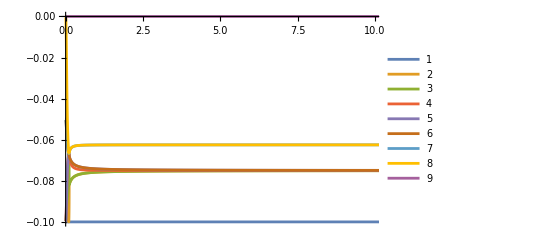

```mathematica
ListLinePlot[data[[All,{1,#}]]&/@Range[2,Length[data[[1]]],2],PlotLegends->Automatic]
```